# Chapter 8 - Problem 3

#### Starting with some constants:

```mathematica
Clear["Global`*"]
h = 6.62607004 * 10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
e = 1.60217 * 10^-19;
nano = 1 * 10^-9;
voltspernano = 1/nano;
```

#### From Chapter 8 - Page 6, we have the following wave equation:

We can use some substitutions so it doesn’t look that long. A and B here are the normalization constant.

```mathematica
F = 0.01 * voltspernano;
L = 1*nano;
alpha = ((2*m*e*F)/ℏ^2)^(1/3);
```

we can use the boundary condition:
ϕ(0) = 0 
since it is an infinite potential well.
Then we can write the wave equation as:

```mathematica
ϕ[z_] = a*AiryAi[alpha*((-en*e)/(e*F) - z)] + b *AiryBi[alpha*((-en*e)/(e*F) - z)];
ϕzero = ϕ[0];
```

```mathematica
Solve[ϕzero == 0, {b}]
```

{{b→-(a AiryAi[-64.0263 en])/AiryBi[-64.0263 en]}}

The above equation is b in terms of a, so we can make that substitution into the equation.

```mathematica
b = -(a *AiryAi[-64.02629444363819 *en])/AiryBi[-64.02629444363819* en];
ϕ[z_] = a*AiryAi[alpha*((-en*e)/(e*F) - z )] + b*AiryBi[alpha*((-en*e)/(e*F)  - z)];
```

#### So the equations below is how you find a:

```mathematica
ψ[z_] = Abs[AiryAi[alpha*((-en*e)/(e*F) - z )]-AiryAi[-64.02629444363819 *en]/AiryBi[-64.02629444363819* en]* AiryBi[alpha*((-en*e)/(e*F)  - z)]];
en = 0.371029;
a = 1/Sqrt[Integrate[Abs[ψ[z]]^2,{z,0,L}]]
```

148219.

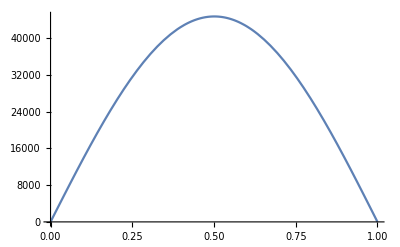

```mathematica
Plot[a*ψ[z],{z,0,L}]
```